```mathematica
(*Malcolm Jardine-02/21 
This notebook takes in external fields from MuMax simulations for a single magnet of dimension x= 230e-9, y= 1000e-9, z=100e-9, and plots a cross section of teh data through the middle of it. 
This does not have fields inside magnet volume.

Can run all the code sequentially and get figure 2 from pressing-control A,shift enter.*)
```

CreateDirectory::filex: C:\Users\Frolov Labuser\Documents\MalcolmJ\MicroMagneticPaperGitHub\Mathematica\Mathematica_out\FieldPlotSingleMag\ already exists.

10427

10826

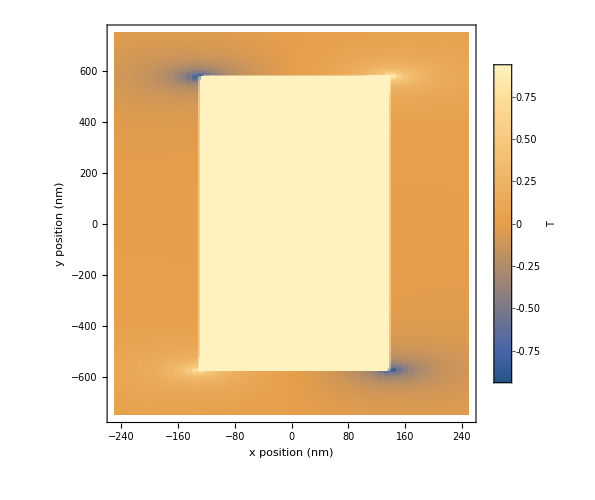

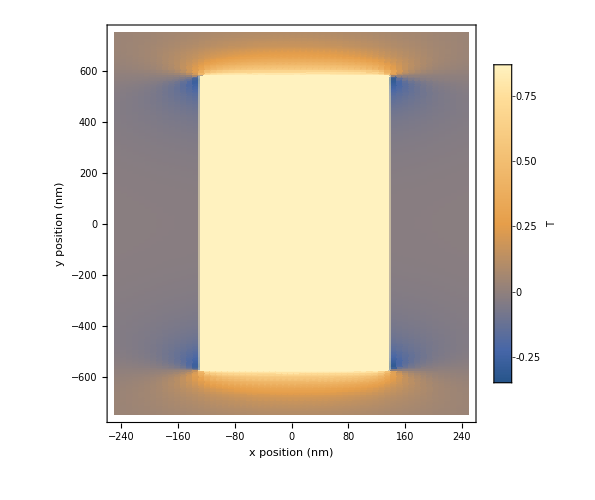

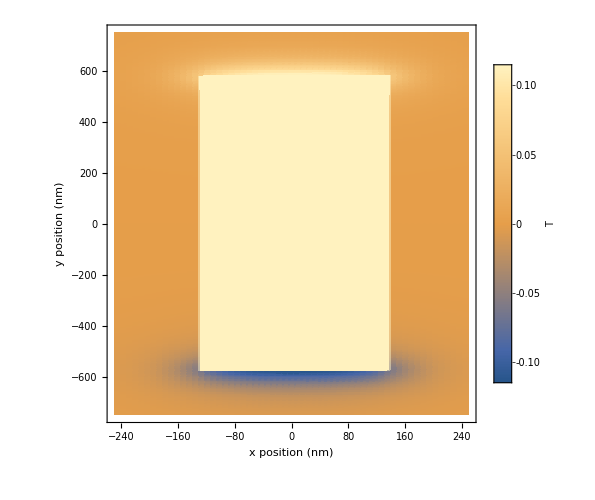

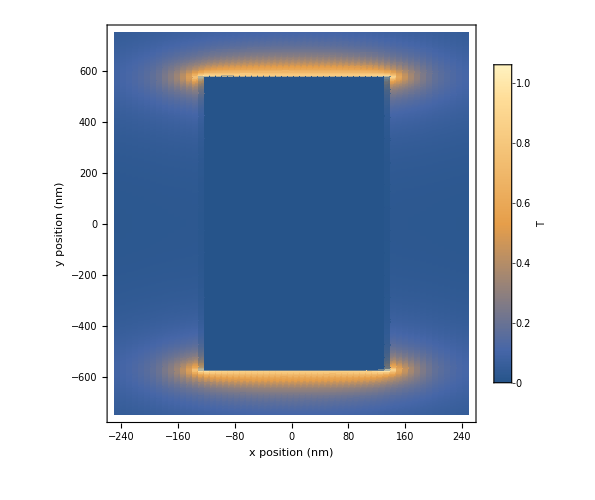

```mathematica
inputfile=ImportString["..\\MuMax3\\Single_Magnet\\B_eff.region7000000.csv"];
FieldData=Import[inputfile,"Data"];
(*FilePrint[inputfile]*)(*Prints out data*)
fileInfo="FieldPlotSingleMag";


SetDirectory[NotebookDirectory[]];
(*Setting where plots are created to current folder where this file is (or telling path to start from here)*)
CreateDirectory[StringJoin[{"Mathematica_out/",fileInfo,"/"}]];


Nx=60;
Ny=400;
Nz=10;

zlayer=4;

numZerosStart=1;
numZerosEnd=0;

TopRowStart=numZerosStart+zlayer*Ny+zlayer; (*Row to start ON*)
TopRowEnd=Ny-numZerosEnd+zlayer*Ny+zlayer;

TopRowStarty=numZerosStart+zlayer*Ny+zlayer+(Nz+1+(Nz+1)*Ny);
TopRowEndy=Ny-numZerosEnd+zlayer*Ny+zlayer+(Nz+1+(Nz+1)*Ny);

TopRowStartz=numZerosStart+zlayer*Ny+zlayer+2*(Nz+1+(Nz+1)*Ny)
TopRowEndz=Ny-numZerosEnd+zlayer*Ny+zlayer+2*(Nz+1+(Nz+1)*Ny)


Bx=FieldData[[TopRowStart;;TopRowEnd,1;;Nx]];
By=FieldData[[TopRowStarty;;TopRowEndy,1;;Nx]];
Bz=FieldData[[TopRowStartz;;TopRowEndz,1;;Nx]];
BxNan=Bx/.x_/;x==0->3*Max[Bx];
ByNan=By/.x_/;x==0->3*Max[By];
BzNan=Bz/.x_/;x==0->3*Max[Bz];
(*BxNan=Bx/.x_/;x==0->NaN;*)

Bmag=Sqrt[Bx^2+By^2+Bz^2];

(*xDistance=heatMapData[[lengthOfData,11]]*10^9;(*Taking max of x distance covered and finding range*)
yDistance=heatMapData[[lengthOfData,12]]*10^9;(*Only records y at end of regions*)*)

xDistance=500;(*Taking max of x distance covered and finding range*)
yDistance=1500;(*Only records y at end of regions*)


BxPlot=ListDensityPlot[BxNan,DataRange->{{-xDistance/2,xDistance/2},{-yDistance/2,yDistance/2}},ClippingStyle->Blue,PlotLegends->BarLegend[Automatic,LegendLabel->"T"],PlotRange->{Min[Bx],Max[Bx]},(*PlotLabel->StringJoin[{"Bx-",PlotLabelName}],*)LabelStyle->{FontFamily->"Helvetica",20,GrayLevel[0]},ImageSize->500,Frame->True,FrameLabel->{{HoldForm["y position (nm)"],None},{HoldForm["x position (nm)"],None}},FrameStyle->Directive[Black,Thickness[Small]]]

ByPlot=ListDensityPlot[ByNan,DataRange->{{-xDistance/2,xDistance/2},{-yDistance/2,yDistance/2}},ClippingStyle->Blue,PlotLegends->BarLegend[Automatic,LegendLabel->"T"],PlotRange->{Min[By],Max[By]},(*PlotLabel->StringJoin[{"Bx-",PlotLabelName}],*)LabelStyle->{FontFamily->"Helvetica",20,GrayLevel[0]},ImageSize->500,Frame->True,FrameLabel->{{HoldForm["y position (nm)"],None},{HoldForm["x position (nm)"],None}},FrameStyle->Directive[Black,Thickness[Small]]]

BzPlot=ListDensityPlot[BzNan,DataRange->{{-xDistance/2,xDistance/2},{-yDistance/2,yDistance/2}},ClippingStyle->Blue,PlotLegends->BarLegend[Automatic,LegendLabel->"T"],PlotRange->{Min[Bz],Max[Bz]},(*PlotLabel->StringJoin[{"Bx-",PlotLabelName}],*)LabelStyle->{FontFamily->"Helvetica",20,GrayLevel[0]},ImageSize->500,Frame->True,FrameLabel->{{HoldForm["y position (nm)"],None},{HoldForm["x position (nm)"],None}},FrameStyle->Directive[Black,Thickness[Small]]]

(*BmagPlot=ListDensityPlot[Bmag,DataRange->{{-xDistance/2,xDistance/2},{-yDistance/2,yDistance/2}},ClippingStyle->Blue,PlotLegends->BarLegend[Automatic,LegendLabel->"T"],PlotRange->{Min[Bmag],Max[Bmag]},(*PlotLabel->StringJoin[{"Bx-",PlotLabelName}],*)LabelStyle->{FontFamily->"Helvetica",20,GrayLevel[0]},ImageSize->500,Frame->True,FrameLabel->{{HoldForm["y position (nm)"],None},{HoldForm["x position (nm)"],None}},FrameStyle->Directive[Black,Thickness[Small]]]*)

BmagPlot=ListDensityPlot[Bmag,DataRange->{{-xDistance/2,xDistance/2},{-yDistance/2,yDistance/2}},ClippingStyle->Blue,PlotLegends->BarLegend[Automatic,LegendLabel->"T"],PlotRange->{Min[Bmag],Max[Bmag]},(*PlotLabel->StringJoin[{"Bx-",PlotLabelName}],*)LabelStyle->{FontFamily->"Helvetica",24,GrayLevel[0]},ImageSize->500,(*Frame->True,*)FrameLabel->{{HoldForm["y position (nm)"],None},{HoldForm["x position (nm)"],None}},FrameStyle->Directive[Black,Thickness[Small]]]
```

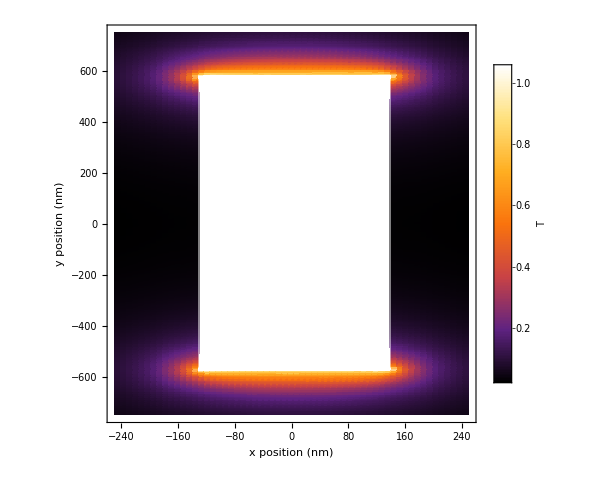

```mathematica
Bmag=Sqrt[Bx^2+By^2+Bz^2];
BmagNan=Bmag/.x_/;x==0->3*Max[Bmag];

BmagPlot=ListDensityPlot[BmagNan,DataRange->{{-xDistance/2,xDistance/2},{-yDistance/2,yDistance/2}},ClippingStyle->RGBColor[120/255,120/255,120/255],PlotLegends->BarLegend[Automatic,LegendLabel->"T"],PlotRange->{Min[Bmag],Max[Bmag]},(*PlotLabel->StringJoin[{"Bx-",PlotLabelName}],*)LabelStyle->{FontFamily->"Helvetica",24,GrayLevel[0]},ImageSize->500,(*Frame->True,*)FrameLabel->{{HoldForm["y position (nm)"],None},{HoldForm["x position (nm)"],None}}(*,FrameStyle->Directive[Black,Thickness[Small]]*),ColorFunction->"SunsetColors"]

(*Export[StringJoin[{"Mathematica_out/",fileInfo,"/","Bmag_SingleMagnetX230Y1000Z100_slice50nm.eps"}],BmagPlot];*)
Export[StringJoin[{"Mathematica_out/",fileInfo,"/","Bmag_SingleMagnetX230Y1000Z100_slice50nm.png"}],BmagPlot];
```